```mathematica
Sunrise[]
```

Minute: Sun 22 Sep 2019 06:43GMT-7.

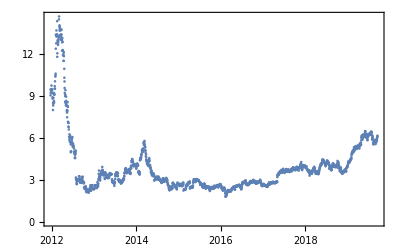

```mathematica
DateListPlot[
FinancialData["NASDAQ:ZNGA","Price",All]
,PlotRange->Full,ImageSize->Full,PlotTheme->"Detailed",ColorFunction->"DarkRainbow",Joined->False
]
```

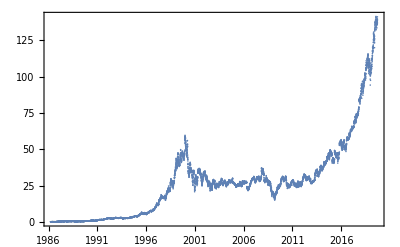

```mathematica
DateListPlot[
FinancialData["NASDAQ:MSFT","Price",All]
,PlotRange->Full,ImageSize->Full,PlotTheme->"Detailed",ColorFunction->"DarkRainbow",Joined->False
]
```

```mathematica
FinancialData["NASDAQ:MSFT","Sector"]
```

Software-Infrastructure

```mathematica
LinguisticAssistant
```

Failure[…]

```mathematica
|
```

```mathematica
Table[LinguisticAssistant,{x,0,10}]
```

{Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…]}

```mathematica
LinguisticAssistant
```

```mathematica
CompanyData["SampleEntities"]
```

{Apple,Pfizer,Novartis,Bank of America,Goldman Sachs Group,Berkshire Hathaway,eBay,Delta Air Lines,AT&T,Monsanto}

```mathematica
Entity["Company","Microsoft"]
```

Entity[Company,Microsoft]

```mathematica
Entity["Company","Apple"]
```

Entity[Company,Apple]

```mathematica
Entity["Financial","NASDAQ:AAPL"]
```

Apple

```mathematica
CompanyData[Entity["Financial","NASDAQ:AAPL"],"Revenue"]
```

CompanyData::notent: Apple is not a known entity, class, or tag for CompanyData. Use CompanyData[] for a list of entities.

CompanyData[Apple,Revenue]

```mathematica
CompanyData[Entity["Company","Apple::5zkjq"],"Revenue"]
```

Missing[UnknownProperty,{Company,Revenue}]

```mathematica
Manipulate[
With[{stock="NASDAQ:AMZN"},
With[{ts=FinancialData[stock,"Price",All]},
DateListPlot[
Map[
Function[s,
{First@First@s,Total@Map[Last,s]}
],Partition[
Transpose[{
ts["Dates"][[;;-2]],
Differences@ts["Values"]
}],i]]
,PlotTheme->"Detailed",PlotRange->Full,ImageSize->Full,Joined->False,ColorFunction->"DarkRainbow"]
]],{i,1,10,1}]
```

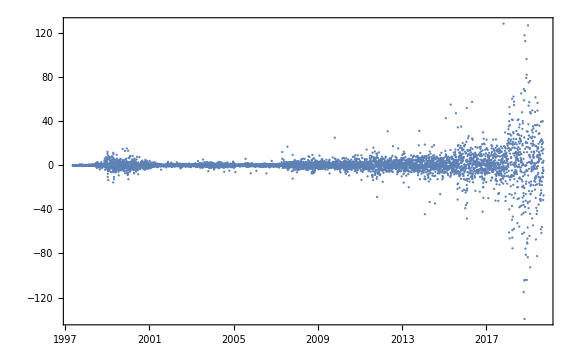
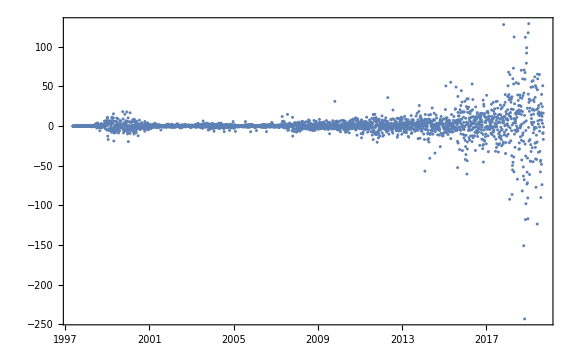
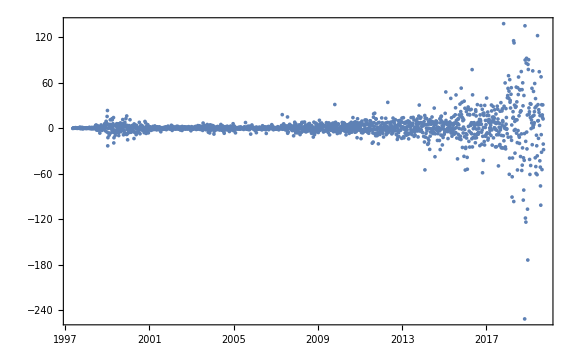
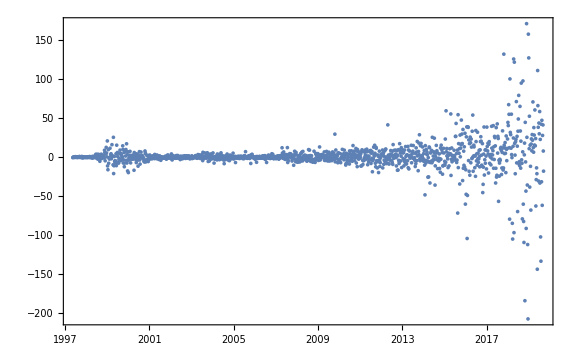
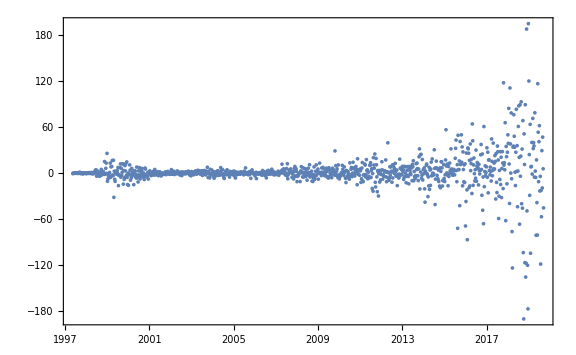
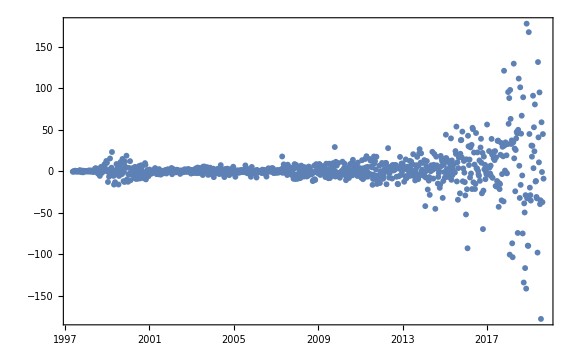
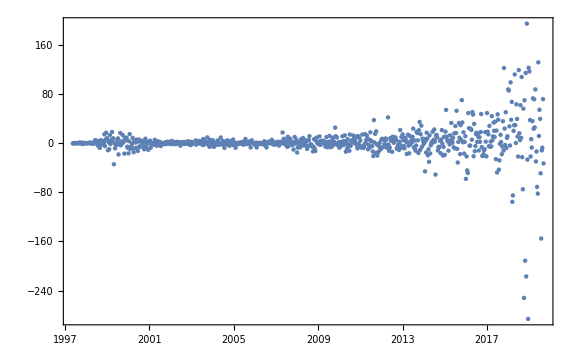
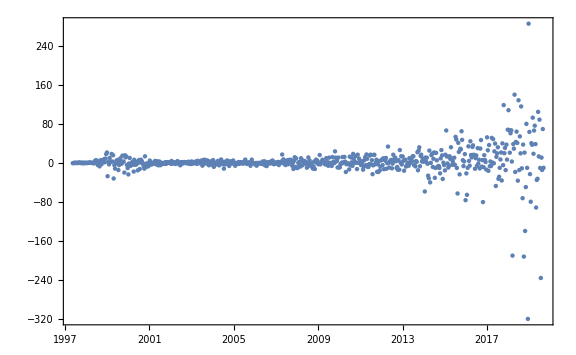

```mathematica
Table[
With[{stock="NASDAQ:AMZN"},
With[{ts=FinancialData[stock,"Price",All]},
DateListPlot[
Map[
Function[s,
{First@First@s,Total@Map[Last,s]}
],Partition[
Transpose[{
ts["Dates"][[;;-2]],
Differences@ts["Values"]
}],i]]
,PlotTheme->"Detailed",PlotRange->Full,ImageSize->Large,Joined->False,ColorFunction->"DarkRainbow"]
]],{i,1,10,1}]
```

Initializing FinancialData indices ....

Initializing FinancialData indices ....

Initializing FinancialData indices ....

«5 more identical outputs»

FinancialData::dlfail: Internet download of data for FinancialData failed. Use Help > Internet Connectivity... to test or reconfigure internet connectivity.

Transpose::nmtx: The first two levels of {$Failed[],Differences[$Failed[Values]]} cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

DateListPlot::ldata: Transpose[] is not a valid dataset or list of datasets.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

DateListPlot::ldata: Transpose[] is not a valid dataset or list of datasets.

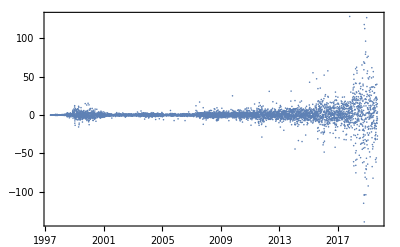
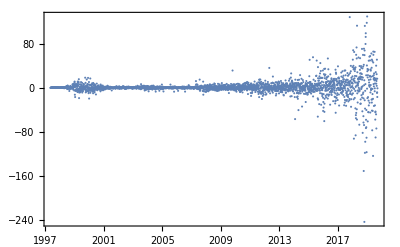
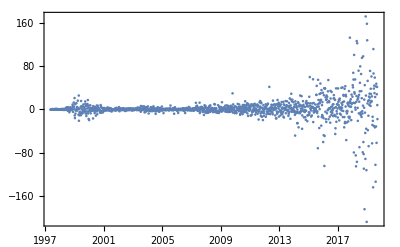
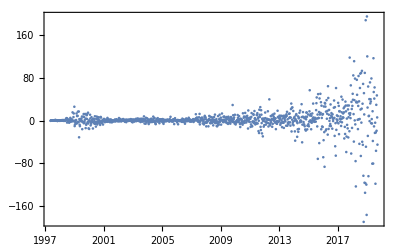
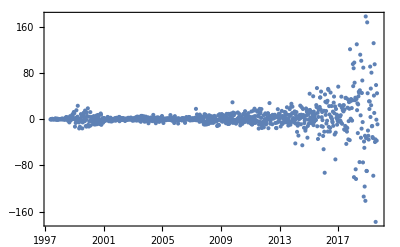
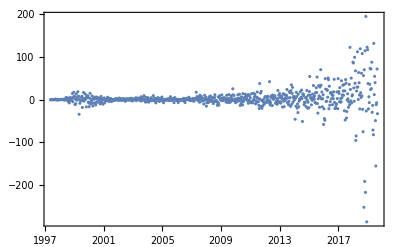
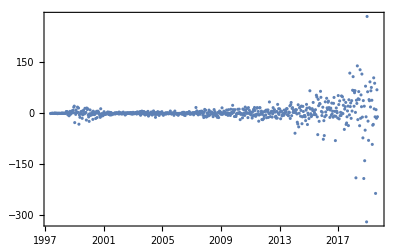
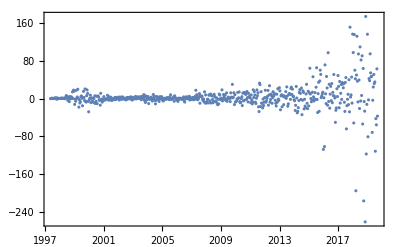
{-Graphics-,-Graphics-,DateListPlot[Transpose[],PlotTheme→Detailed,PlotRange→Full,Joined→False,ColorFunction→DarkRainbow],-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelTable[
With[{stock="NASDAQ:AMZN"},
With[{ts=FinancialData[stock,"Price",All]},
DateListPlot[
Map[
Function[s,
{First@First@s,Total@Map[Last,s]}
],Partition[
Transpose[{
ts["Dates"][[;;-2]],
Differences@ts["Values"]
}],i]]
,PlotTheme->"Detailed",PlotRange->Full,Joined->False,ColorFunction->"DarkRainbow"]
]],{i,1,10,1}]
```

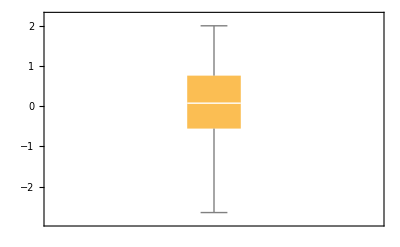

```mathematica
BoxWhiskerChart[RandomVariate[NormalDistribution[0,1],100]]
```

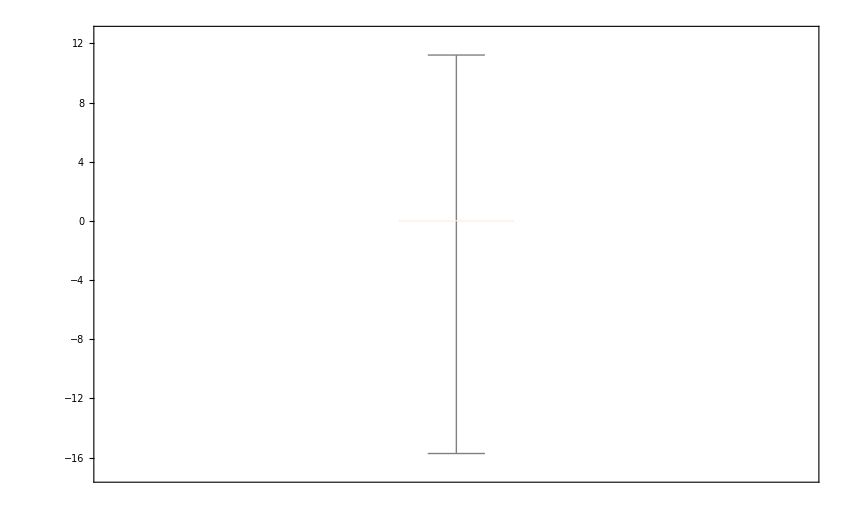

```mathematica
BoxWhiskerChart[Differences@FinancialData["NASDAQ:AAPL","Price",All]["Values"]]
```

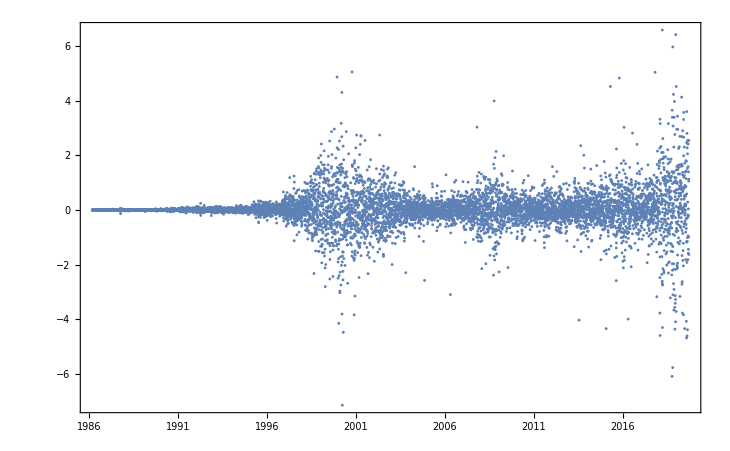
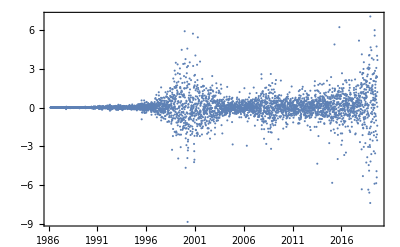
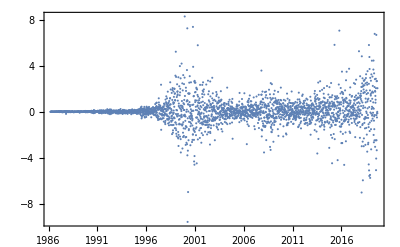
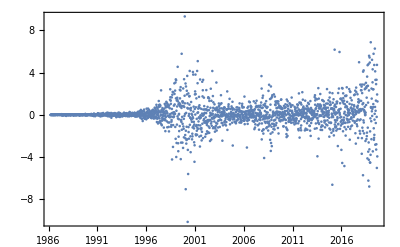
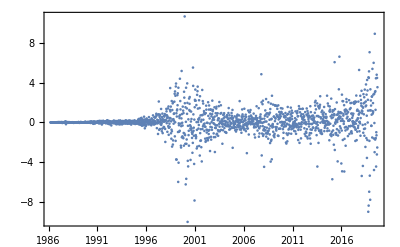
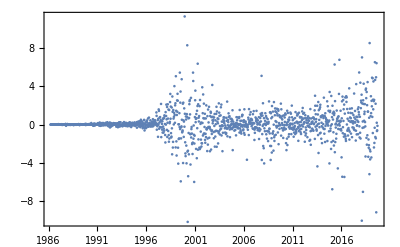
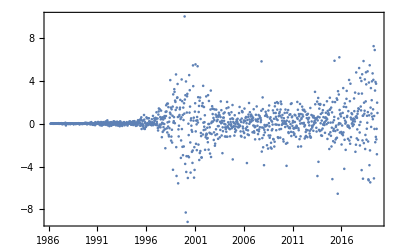
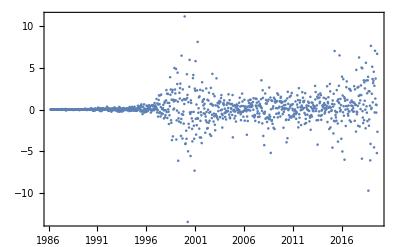

```mathematica
ParallelTable[
With[{stock="NASDAQ:MSFT"},
With[{ts=FinancialData[stock,"Price",All]},
DateListPlot[
Map[
Function[s,
{First@First@s,Total@Map[Last,s]}
],Partition[
Transpose[{
ts["Dates"][[;;-2]],
Differences@ts["Values"]
}],i]]
,PlotTheme->"Detailed",PlotRange->Full,Joined->False,ColorFunction->"DarkRainbow"]
]],{i,1,10,1}]
```

```mathematica
FinancialData["NASDAQ:MSFT","Price"]
```

Missing[NotAvailable]

```mathematica
FinancialData["EUR/USD"]
```

1.103

```mathematica
FinancialData[{"XAU","USD"}]
```

1501.9

```mathematica
FinancialData[{"XAG","USD"}]
```

17.88

```mathematica
FinancialData[{"XPT","USD"}]
```

940.

```mathematica
FinancialData[{"XPD","USD"}]
```

1608.

```mathematica
FinancialData[{"XCP","USD"}]
```

FinancialData::notent: XCP is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

{Missing[NotAvailable],Missing[NotAvailable]}

```mathematica
FinancialData[{"EUR","BRL"}]
```

4.5956

```mathematica
DateListPlot[FinancialData["EUR/USD",All],Joined->True]
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed,1].

DateListPlot::ldata: TimeSeries[Flatten[$Failed,1]] is not a valid dataset or list of datasets.

DateListPlot[TimeSeries[Flatten[$Failed,1]],Joined→True]

```mathematica
FinancialData["EUR/USD",All]
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed,1].

TimeSeries[Flatten[$Failed,1]]

```mathematica
FinancialData[{"USD","EUR"}]
```

0.906618

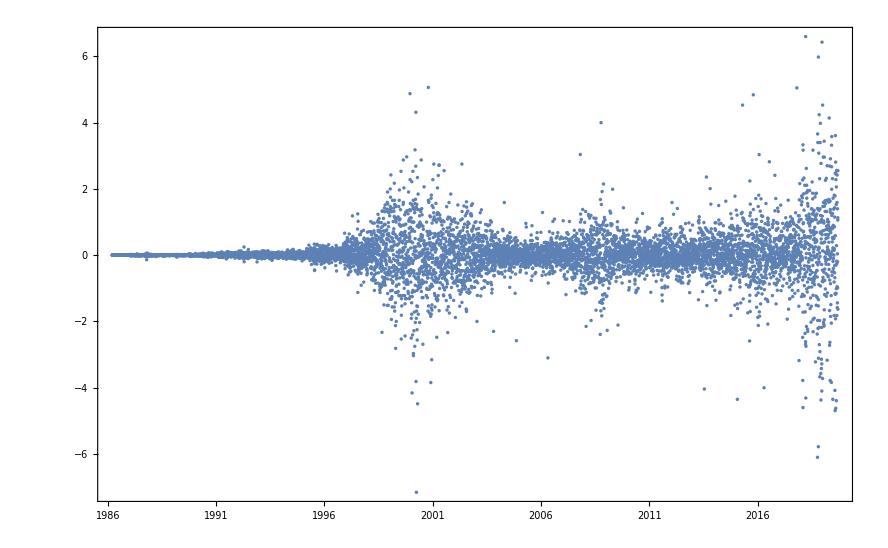

```mathematica
With[{stock="NASDAQ:MSFT"},
With[{ts=FinancialData[stock,"Price",All]},
DateListPlot[
Transpose[{
ts["Dates"][[;;-2]],
Differences@ts["Values"]
}]
,PlotTheme->"Detailed",PlotRange->Full,Joined->False,ColorFunction->"DarkRainbow"]
]]
```

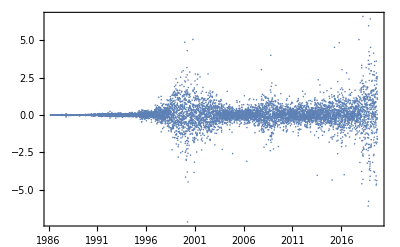

```mathematica
With[{stock="NASDAQ:MSFT"},
With[{ts=FinancialData[stock,"Price",All]},
DateListPlot[
Transpose[{
ts["Dates"][[;;-2]],
Differences@ts["Values"]
}]
,PlotTheme->"Detailed",PlotRange->Full,Joined->False, PlotLegends->"Expressions"]
]]
```

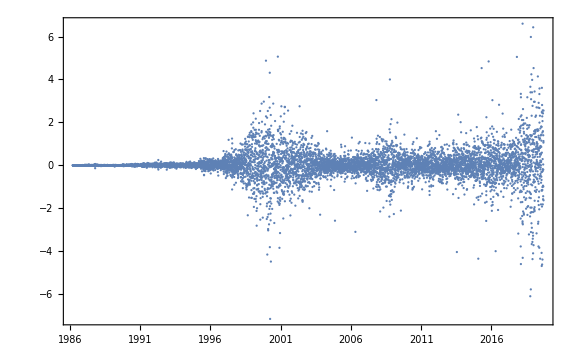

```mathematica
With[{stock="NASDAQ:MSFT"},
With[{ts=FinancialData[stock,"Price",All]},
DateListPlot[
Transpose[{
ts["Dates"][[;;-2]],
Differences@ts["Values"]
}]
,PlotTheme->"Detailed",PlotRange->Full,Joined->False, PlotLegends->"Expressions",ImageSize->Large]
]]
```

```mathematica
With[{stock={"NASDAQ:MSFT","NAS}},
With[{ts=FinancialData[stock,"Price",All]},
DateListPlot[
Transpose[{
ts["Dates"][[;;-2]],
Differences@ts["Values"]
}]
,PlotTheme→"Detailed",PlotRange→Full,Joined→False, PlotLegends→"Expressions",ImageSize→Large]{"NASDAQ:MSFT","NASDAQ:GOOGL","NASDAQ:FB","NASDAQ:BIDU","NASDAQ:NTES","NASDAQ:VRSN","NASDAQ:MTCH","NASDAQ:IAC","NASDAQ:CRWD","NASDAQ:IQ","NASDAQ:SSNC","NASDAQ:CT
]]
```

```mathematica
{"NASDAQ:MSFT","NASDAQ:GOOGL","NASDAQ:FB","NASDAQ:BIDU","NASDAQ:NTES","NASDAQ:VRSN","NASDAQ:MTCH","NASDAQ:IAC","NASDAQ:CRWD","NASDAQ:IQ","NASDAQ:SSNC","NASDAQ:CTXS","NASDAQ:YNDX","NASDAQ:OKTA","NASDAQ:WB","NASDAQ:DOX","NASDAQ:DBX","NASDAQ:COUP","NASDAQ:FFIV","NASDAQ:MOMO","NASDAQ:ZS","NASDAQ:WIX","NASDAQ:YY","NASDAQ:BILI","NASDAQ:NTNX","NASDAQ:JCOM","NASDAQ:CYBR","NASDAQ:ANGI","NASDAQ:CARG","NASDAQ:FIVN","NASDAQ:APPN","NASDAQ:SINA","NASDAQ:LEXEA","NASDAQ:BL","NASDAQ:LEXEB","NASDAQ:LPSN","NASDAQ:ALTR","NASDAQ:EVOP","NASDAQ:MIME","NASDAQ:TENB","NASDAQ:VRNS","NASDAQ:CSGS","NASDAQ:BAND","NASDAQ:GRPN","NASDAQ:UPWK","NASDAQ:GSKY","NASDAQ:LKCO","NASDAQ:CRTO","NASDAQ:OPRA","NASDAQ:TLND","NASDAQ:TWOU","NASDAQ:QTT","NASDAQ:UXIN","NASDAQ:SPNS","NASDAQ:CDLX","NASDAQ:JFIN","NASDAQ:LTRPA","NASDAQ:TTGT","NASDAQ:LTRPB","NASDAQ:QNST","NASDAQ:TCX","NASDAQ:EVER","NASDAQ:IIIV","NASDAQ:CARB","NASDAQ:SOHU","NASDAQ:USAT","NASDAQ:PRTH","NASDAQ:TRUE","NASDAQ:LLNW","NASDAQ:MEET","NASDAQ:TNAV","NASDAQ:XELA","NASDAQ:TC","NASDAQ:PCOM","NASDAQ:MAMS","NASDAQ:TZOO","NASDAQ:PERI","NASDAQ:CYRN","NASDAQ:VERI","NASDAQ:SREV","NASDAQ:SYNC","NASDAQ:MARK","NASDAQ:MNDO","NASDAQ:PYDS","NASDAQ:AUTO","NASDAQ:SPRT","NASDAQ:MOXC","NASDAQ:CCIH","NASDAQ:NETE","NASDAQ:DLPN","NASDAQ:IZEA","NASDAQ:IPDN"}
```

{NASDAQ:MSFT,NASDAQ:GOOGL,NASDAQ:FB,NASDAQ:BIDU,NASDAQ:NTES,NASDAQ:VRSN,NASDAQ:MTCH,NASDAQ:IAC,NASDAQ:CRWD,NASDAQ:IQ,NASDAQ:SSNC,NASDAQ:CTXS,NASDAQ:YNDX,NASDAQ:OKTA,NASDAQ:WB,NASDAQ:DOX,NASDAQ:DBX,NASDAQ:COUP,NASDAQ:FFIV,NASDAQ:MOMO,NASDAQ:ZS,NASDAQ:WIX,NASDAQ:YY,NASDAQ:BILI,NASDAQ:NTNX,NASDAQ:JCOM,NASDAQ:CYBR,NASDAQ:ANGI,NASDAQ:CARG,NASDAQ:FIVN,NASDAQ:APPN,NASDAQ:SINA,NASDAQ:LEXEA,NASDAQ:BL,NASDAQ:LEXEB,NASDAQ:LPSN,NASDAQ:ALTR,NASDAQ:EVOP,NASDAQ:MIME,NASDAQ:TENB,NASDAQ:VRNS,NASDAQ:CSGS,NASDAQ:BAND,NASDAQ:GRPN,NASDAQ:UPWK,NASDAQ:GSKY,NASDAQ:LKCO,NASDAQ:CRTO,NASDAQ:OPRA,NASDAQ:TLND,NASDAQ:TWOU,NASDAQ:QTT,NASDAQ:UXIN,NASDAQ:SPNS,NASDAQ:CDLX,NASDAQ:JFIN,NASDAQ:LTRPA,NASDAQ:TTGT,NASDAQ:LTRPB,NASDAQ:QNST,NASDAQ:TCX,NASDAQ:EVER,NASDAQ:IIIV,NASDAQ:CARB,NASDAQ:SOHU,NASDAQ:USAT,NASDAQ:PRTH,NASDAQ:TRUE,NASDAQ:LLNW,NASDAQ:MEET,NASDAQ:TNAV,NASDAQ:XELA,NASDAQ:TC,NASDAQ:PCOM,NASDAQ:MAMS,NASDAQ:TZOO,NASDAQ:PERI,NASDAQ:CYRN,NASDAQ:VERI,NASDAQ:SREV,NASDAQ:SYNC,NASDAQ:MARK,NASDAQ:MNDO,NASDAQ:PYDS,NASDAQ:AUTO,NASDAQ:SPRT,NASDAQ:MOXC,NASDAQ:CCIH,NASDAQ:NETE,NASDAQ:DLPN,NASDAQ:IZEA,NASDAQ:IPDN}

```mathematica
ParallelMap[FinancialData[#,"Price",All]&,Out[38]]
```

{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}

```mathematica
Transpose[{Out[38],Out[39]}]
```

{{NASDAQ:MSFT,TimeSeries[…]},{NASDAQ:GOOGL,TimeSeries[…]},{NASDAQ:FB,TimeSeries[…]},{NASDAQ:BIDU,TimeSeries[…]},{NASDAQ:NTES,TimeSeries[…]},{NASDAQ:VRSN,TimeSeries[…]},{NASDAQ:MTCH,TimeSeries[…]},{NASDAQ:IAC,TimeSeries[…]},{NASDAQ:CRWD,TimeSeries[…]},{NASDAQ:IQ,TimeSeries[…]},{NASDAQ:SSNC,TimeSeries[…]},{NASDAQ:CTXS,TimeSeries[…]},{NASDAQ:YNDX,TimeSeries[…]},{NASDAQ:OKTA,TimeSeries[…]},{NASDAQ:WB,TimeSeries[…]},{NASDAQ:DOX,TimeSeries[…]},{NASDAQ:DBX,TimeSeries[…]},{NASDAQ:COUP,TimeSeries[…]},{NASDAQ:FFIV,TimeSeries[…]},{NASDAQ:MOMO,TimeSeries[…]},{NASDAQ:ZS,TimeSeries[…]},{NASDAQ:WIX,TimeSeries[…]},{NASDAQ:YY,TimeSeries[…]},{NASDAQ:BILI,TimeSeries[…]},{NASDAQ:NTNX,TimeSeries[…]},{NASDAQ:JCOM,TimeSeries[…]},{NASDAQ:CYBR,TimeSeries[…]},{NASDAQ:ANGI,TimeSeries[…]},{NASDAQ:CARG,TimeSeries[…]},{NASDAQ:FIVN,TimeSeries[…]},{NASDAQ:APPN,TimeSeries[…]},{NASDAQ:SINA,TimeSeries[…]},{NASDAQ:LEXEA,TimeSeries[…]},{NASDAQ:BL,TimeSeries[…]},{NASDAQ:LEXEB,TimeSeries[…]},{NASDAQ:LPSN,TimeSeries[…]},{NASDAQ:ALTR,TimeSeries[…]},{NASDAQ:EVOP,TimeSeries[…]},{NASDAQ:MIME,TimeSeries[…]},{NASDAQ:TENB,TimeSeries[…]},{NASDAQ:VRNS,TimeSeries[…]},{NASDAQ:CSGS,TimeSeries[…]},{NASDAQ:BAND,TimeSeries[…]},{NASDAQ:GRPN,TimeSeries[…]},{NASDAQ:UPWK,TimeSeries[…]},{NASDAQ:GSKY,TimeSeries[…]},{NASDAQ:LKCO,TimeSeries[…]},{NASDAQ:CRTO,TimeSeries[…]},{NASDAQ:OPRA,TimeSeries[…]},{NASDAQ:TLND,TimeSeries[…]},{NASDAQ:TWOU,TimeSeries[…]},{NASDAQ:QTT,TimeSeries[…]},{NASDAQ:UXIN,TimeSeries[…]},{NASDAQ:SPNS,TimeSeries[…]},{NASDAQ:CDLX,TimeSeries[…]},{NASDAQ:JFIN,TimeSeries[…]},{NASDAQ:LTRPA,TimeSeries[…]},{NASDAQ:TTGT,TimeSeries[…]},{NASDAQ:LTRPB,TimeSeries[…]},{NASDAQ:QNST,TimeSeries[…]},{NASDAQ:TCX,TimeSeries[…]},{NASDAQ:EVER,TimeSeries[…]},{NASDAQ:IIIV,TimeSeries[…]},{NASDAQ:CARB,TimeSeries[…]},{NASDAQ:SOHU,TimeSeries[…]},{NASDAQ:USAT,TimeSeries[…]},{NASDAQ:PRTH,TimeSeries[…]},{NASDAQ:TRUE,TimeSeries[…]},{NASDAQ:LLNW,TimeSeries[…]},{NASDAQ:MEET,TimeSeries[…]},{NASDAQ:TNAV,TimeSeries[…]},{NASDAQ:XELA,TimeSeries[…]},{NASDAQ:TC,TimeSeries[…]},{NASDAQ:PCOM,TimeSeries[…]},{NASDAQ:MAMS,TimeSeries[…]},{NASDAQ:TZOO,TimeSeries[…]},{NASDAQ:PERI,TimeSeries[…]},{NASDAQ:CYRN,TimeSeries[…]},{NASDAQ:VERI,TimeSeries[…]},{NASDAQ:SREV,TimeSeries[…]},{NASDAQ:SYNC,TimeSeries[…]},{NASDAQ:MARK,TimeSeries[…]},{NASDAQ:MNDO,TimeSeries[…]},{NASDAQ:PYDS,TimeSeries[…]},{NASDAQ:AUTO,TimeSeries[…]},{NASDAQ:SPRT,TimeSeries[…]},{NASDAQ:MOXC,TimeSeries[…]},{NASDAQ:CCIH,TimeSeries[…]},{NASDAQ:NETE,TimeSeries[…]},{NASDAQ:DLPN,TimeSeries[…]},{NASDAQ:IZEA,TimeSeries[…]},{NASDAQ:IPDN,TimeSeries[…]}}